```mathematica
2+2
```

4

```mathematica
1234+34567
```

35801

```mathematica
10^3
```

1000

```mathematica
Plus[2,100000]
```

100002

```mathematica
Plus[2,100000]^3
```

1000060001200008

```mathematica
Times[10,156]
```

1560

```mathematica
Plus[2^3,4^5]
```

1032

```mathematica
RandomInteger[100]
```

95

```mathematica
Plus[RandomInteger[10],RandomInteger[10]]
```

8

```mathematica
Plus[RandomInteger[0],RandomInteger[10,20]]
```

{3,8,3,5,6,1,7,4,8,7,5,1,10,3,0,5,4,10,7,2}

```mathematica
Plus[RandomInteger[],RandomInteger[]]
```

1

```mathematica
RandomInteger[{a,b}]
```

RandomInteger::unifr: The endpoints specified by {a,b} for the endpoints of the discrete uniform distribution range are not integers.

RandomInteger[{a,b}]

```mathematica
{1,2,3,4,10,6^3,s,a}
```

{1,2,3,4,10,216,s,a}

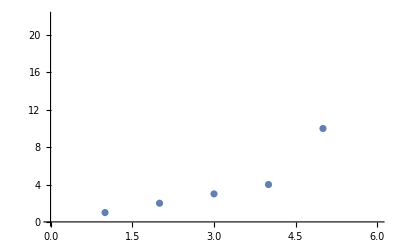

```mathematica
ListPlot[%]
```

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Reverse[Range[100]]
```

{100,99,98,97,96,95,94,93,92,91,90,89,88,87,86,85,84,83,82,81,80,79,78,77,76,75,74,73,72,71,70,69,68,67,66,65,64,63,62,61,60,59,58,57,56,55,54,53,52,51,50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
a = Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

{10,9,8,7,6,5,4,3,2,1}

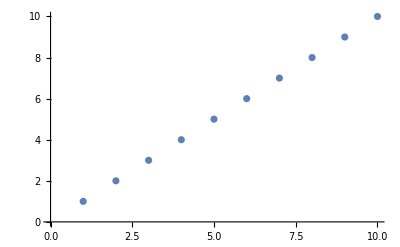

```mathematica
b = Reverse[a]
ListPlot[a]
```

```mathematica
ListPlot[a,b]
```

ListPlot::nonopt: Options expected (instead of {10,9,8,7,6,5,4,3,2,1}) beyond position 1 in ListPlot[{1,2,3,4,5,6,7,8,9,10},{10,9,8,7,6,5,4,3,2,1}]. An option must be a rule or a list of rules.

ListPlot[{1,2,3,4,5,6,7,8,9,10},{10,9,8,7,6,5,4,3,2,1}]

```mathematica
a+b
```

{11,11,11,11,11,11,11,11,11,11}

```mathematica
a<>b
```

StringJoin::string: String expected at position 1 in 1<>2<>3<>4<>5<>6<>7<>8<>9<>10<>10<>9<>8<>7<>6<>5<>4<>3<>2<>1.

StringJoin::string: String expected at position 2 in 1<>2<>3<>4<>5<>6<>7<>8<>9<>10<>10<>9<>8<>7<>6<>5<>4<>3<>2<>1.

StringJoin::string: String expected at position 3 in 1<>2<>3<>4<>5<>6<>7<>8<>9<>10<>10<>9<>8<>7<>6<>5<>4<>3<>2<>1.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

1<>2<>3<>4<>5<>6<>7<>8<>9<>10<>10<>9<>8<>7<>6<>5<>4<>3<>2<>1

```mathematica
a = Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
b = Reverse[a]
```

{10,9,8,7,6,5,4,3,2,1}

```mathematica
ListPlot[[a,b]]
```

Part::partd: Part specification ListPlot⟦{1,2,3,4,5,6,7,8,9,10},{10,9,8,7,6,5,4,3,2,1}⟧ is longer than depth of object.

ListPlot⟦{1,2,3,4,5,6,7,8,9,10},{10,9,8,7,6,5,4,3,2,1}⟧

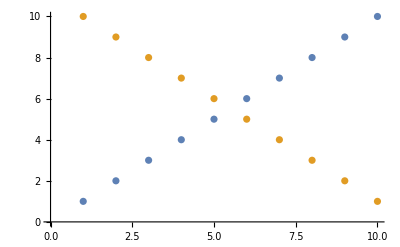

```mathematica
ListPlot[{a,b}]
```

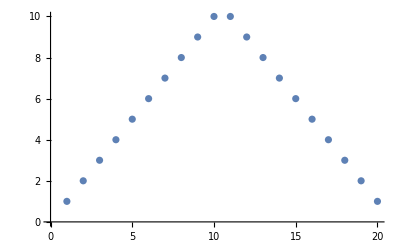

```mathematica
ListPlot[Join[a,b]]
```

```mathematica
Range[RandomInteger[10]]
```

{1}

```mathematica
Range[RandomInteger[10]]
```

{1,2,3,4,5,6,7,8,9}

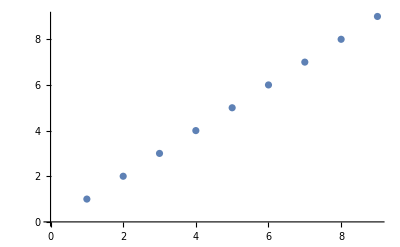

```mathematica
ListPlot[%]
```

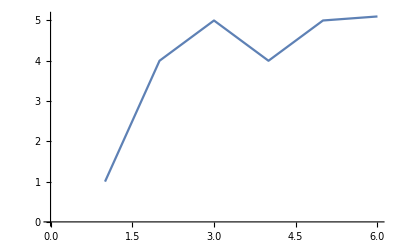

```mathematica
ListLinePlot[{1,4,5,4,5,5.1}]
```

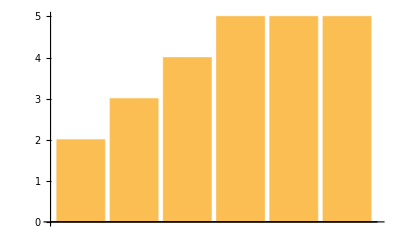

```mathematica
BarChart[{2,3,4,5,5.000001,5.000002}]
```

```mathematica
a = {1,2,3,5,6,9,7,54}
```

{1,2,3,5,6,9,7,54}

```mathematica
PieChart[a]
```

-Graphics-

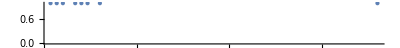

```mathematica
NumberLinePlot[a]
```

```mathematica
Column[a]
```

1
2
3
5
6
9
7
54

```mathematica
a=Range[3]
b = Range[5]
PieChart[[a],[b]]
```

{1,2,3}

{1,2,3,4,5}

```mathematica
PieChart[a,b]
```

PieChart::nonopt: Options expected (instead of {1,2,3,4,5}) beyond position 1 in PieChart[{1,2,3},{1,2,3,4,5}]. An option must be a rule or a list of rules.

```mathematica
a = PieChart[a]
b = PieChart[b]
```

```mathematica
{a,b}
```

{{1,2,3},{1,2,3,4,5}}

```mathematica
{PieChart[a],PieChart[b]}
```

```mathematica
a
```

{1,2,3}

```mathematica
b
```

{1,2,3,4,5}

```mathematica
{PieChart[Range[3]],PieChart[Range[5]]}
```

{-Graphics-,-Graphics-}

```mathematica
{PieChart[a],PieChart[b]}
```

{-Graphics-,-Graphics-}

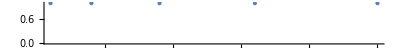

```mathematica
NumberLinePlot[Range[5]^2]
```

```mathematica
a *b
```

Thread::tdlen: Objects of unequal length in {1,2,3} {1,2,3,4,5} cannot be combined.

{1,2,3} {1,2,3,4,5}

```mathematica
a = {1,2,3,4,5}
b = {42,4,2,54,5}
```

{1,2,3,4,5}

{42,4,2,54,5}

```mathematica
a.b
```

297

```mathematica
a*b
```

{42,8,6,216,25}

```mathematica
c = {{1,2},{3,4}}
%//MatrixForm
```

{{1,2},{3,4}}

(1 | 2
3 | 4)

```mathematica
c//MatrixForm
```

(1 | 2
3 | 4)

```mathematica
e = ({{1, 3, 4}, {2, 4, 3}, {4, 5, 5}})
```

{{1,3,4},{2,4,3},{4,5,5}}

```mathematica
Sort[e]
```

{{1,3,4},{2,4,3},{4,5,5}}

```mathematica
a = {1,2,4,3,6,7,3,6,87}
Sort[a]
```

{1,2,4,3,6,7,3,6,87}

{1,2,3,3,4,6,6,7,87}

```mathematica
Reverse[%]
```

{87,7,6,6,4,3,3,2,1}

```mathematica
Plot[{Sin[x],{x,-2Pi,2Pi}},{Cos[x],{x,-2Pi,2Pi}}]
```

Plot::pllim: Range specification {Cos[x],{x,-2 π,2 π}} is not of the form {x, xmin, xmax}.

Plot[{Sin[x],{x,-2 π,2 π}},{Cos[x],{x,-2 π,2 π}}]

```mathematica
Plot[{Sin[x],{x,-2Pi,2Pi}}]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

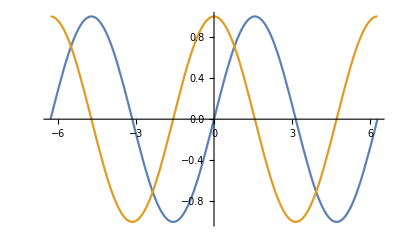

```mathematica
Plot[{Sin[x],Cos[x]},{x,-2 π,2 π}] (*yang jadi list itu fungsinya aja! bukan batas2nya, oiya kalo mau nulis Pi ya Pi terus Esc*)
```

```mathematica
?Export
```

Export[file.ext,expr] exports data to a file, converting it to the format corresponding to the file extension ext. 
Export[file,expr,format] exports data in the specified format.
Export[file,exprs,elems] exports data by treating exprs as elements specified by elems.

```mathematica
ImageIdentify[-Graphics-,car]
```

ImageIdentify::catinv: car is not a valid object category.

ImageIdentify[-Graphics-,car]

plot three dimension

WolframAlpha::timeout: The call to WolframAlpha[plot three dimension,MathematicaParse] has exceeded 30. seconds. Increasing the value of the TimeConstraint option may improve the result.

solve X^2+8 equal to 14

WolframAlpha::timeout: The call to WolframAlpha[solve X^2+8 equal to 14,MathematicaParse] has exceeded 30. seconds. Increasing the value of the TimeConstraint option may improve the result.

```mathematica
Total[Range[10]]
```

55

```mathematica
mylist = {a,4,6,d,4}
```

{a,4,6,d,4}

```mathematica
mylist[[2]]
```

4

```mathematica
Part[mylist,4]
```

d

```mathematica
First[mylist]
```

```mathematica
Rest[mylist]
```

{4,6,d,4}

```mathematica
mylist[[2;;5]]
```

{4,6,d,4}

```mathematica
a = {{1,2},{3,4}};
```

```mathematica
a[[2,All]]
```

{3,4}

```mathematica
Transpose[a]
```

{{1,3},{2,4}}

```mathematica
Inverse[a]
```

{{-2,1},{3/2,-1/2}}

```mathematica
MatrixForm[%]
```

(-2 | 1
3/2 | -1/2)

```mathematica
Length[a]
```

2

```mathematica
2^100
```

1267650600228229401496703205376

```mathematica
?first ten digit
```

Information::notfound: Symbol first not found.

Information::notfound: Symbol ten not found.

Information::notfound: Symbol digit not found.

General::stop: Further output of Information::notfound will be suppressed during this calculation.

```mathematica
IntegerDigits[2^100,10]
```

{1,2,6,7,6,5,0,6,0,0,2,2,8,2,2,9,4,0,1,4,9,6,7,0,3,2,0,5,3,7,6}

```mathematica
Take[%,10]
```

{1,2,6,7,6,5,0,6,0,0}

```mathematica
N[Pi,10]
```

3.141592654

```mathematica
mystring = "I am Ardhi and he is Iqbal"
```

I am Ardhi and he is Iqbal

```mathematica
?String
```

String is the head of a character string "text".

```mathematica
7^200
```

10461838291314357175018899611816813659819188550170233659950140084035125767424262251774382614909364050293065248252546314174063180343683591188150754267339816534637456120001

```mathematica
Count[IntegerDigits[7^200],0]
```

18

```mathematica
Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
Take[%,{10,20}]
```

{10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Take[Drop[Range[100],-80],-10]
```

{11,12,13,14,15,16,17,18,19,20}

```mathematica
Sort[Join[Range[5]^2,Range[5]^3]]
```

{1,1,4,8,9,16,25,27,64,125}

```mathematica
Table[i,5]
```

{i,i,i,i,i}

```mathematica
Table[i,{i,5}]
```

{1,2,3,4,5}

```mathematica
Table[Prime[n],{n,100}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

```mathematica
Table[2i-1,{i,15}]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29}

```mathematica
{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29}
Length[%]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29}

15

```mathematica
Table[Subscript[x,(10i+j)],{i,3},{j,3}]
```

{{x_11,x_12,x_13},{x_21,x_22,x_23},{x_31,x_32,x_33}}

```mathematica
MatrixForm[%] (* atau ctrl +underscore*)
```

(x_11 | x_12 | x_13
x_21 | x_22 | x_23
x_31 | x_32 | x_33)

```mathematica
Table[Subscript[x, i,j],{i,3},{j,3}]//MatrixForm
```

(x_(1,1) | x_(1,2) | x_(1,3)
x_(2,1) | x_(2,2) | x_(2,3)
x_(3,1) | x_(3,2) | x_(3,3))

```mathematica
?Global`*
```

```mathematica
Clear[a]
```

```mathematica
a
```

a

```mathematica
Table[Column[Range[n]],{n,8}]
```

{1,1
2,1
2
3,1
2
3
4,1
2
3
4
5,1
2
3
4
5
6,1
2
3
4
5
6
7,1
2
3
4
5
6
7
8}

```mathematica
Table[PieChart[Table[1,n]],{n,5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Range[0,10,0.001]
```

{0.,0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,0.02,0.021,0.022,0.023,0.024,0.025,0.026,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.041,0.042,0.043,0.044,9911,9.956,9.957,9.958,9.959,9.96,9.961,9.962,9.963,9.964,9.965,9.966,9.967,9.968,9.969,9.97,9.971,9.972,9.973,9.974,9.975,9.976,9.977,9.978,9.979,9.98,9.981,9.982,9.983,9.984,9.985,9.986,9.987,9.988,9.989,9.99,9.991,9.992,9.993,9.994,9.995,9.996,9.997,9.998,9.999,10.}
 |  |  |  |

```mathematica
Table[First[IntegerDigits[n^3]],{n,20}]
```

{1,8,2,6,1,2,3,5,7,1,1,1,2,2,3,4,4,5,6,8}

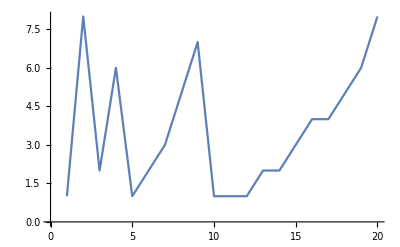

```mathematica
ListLinePlot[%]
```

```mathematica
Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

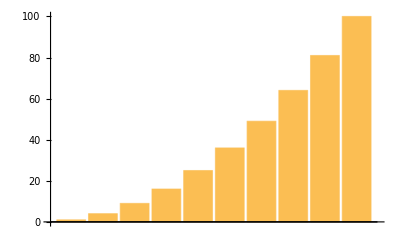

```mathematica
BarChart[%]
```

```mathematica
Show[%105,AxesStyle->Gray]
```

```mathematica
x/.Solve[x+3==7,x][[1]]
```

4

```mathematica
x+3/.x->solution
```

3+solution

```mathematica
ruben@nabenta-indonesia.com
```